```mathematica
Exit[]
```

```mathematica
$Assumptions=b>0&&mpr<0&&μ>0&&σ>0&&a ∈ Reals&&1>k1≥0&&k0≥0&&S0>0&&K>0&&r≥0&&b ∈ Reals&& rf≥0&& γ>0;
```

```mathematica
xx[W_,t_]:=Exp[  W+(mpr-1/2)t^2]-1;
```

```mathematica
γ=.2;mpr=-0.2;
g[a_,t_,b_]:=NIntegrate[Exp[-a xx[w t,t]-w^2/2],{w,-b,b}];
gs[a_,t_,b_]:=NIntegrate[Exp[-a xx[w t,t]-w^2/2]xx[w t,t],{w,-b,b}];
h[a_,w_,t_]:=Exp[-w^2/2/t^2]/t(Exp[-a xx[w ,t]]xx[w ,t]+Exp[-a xx[-w,t]]xx[-w,t])
gs2[a_,t_,b_]:=NIntegrate[h[a,w,t],{w,0,t b}]
as[t_,b_]:=Quiet[FindRoot[gs[a,t,b]==0,{a,-1,0}][[1,2]]]
```

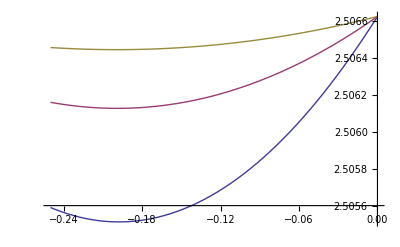

```mathematica
b=5;t=.1;Plot[ {g[a,t 1.5,b],g[a,t,b],g[a,t .6,b]},{a,-.25,0}]
```

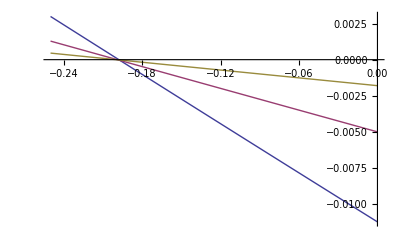

```mathematica
b=5;t=.1;Plot[ {gs[a,t 1.5,b],gs[a,t,b],gs[a,t .6,b]},{a,-.25,0}]
```

```mathematica
as[.1,b]
```

-0.994986

```mathematica
gs2[mpr,t,b]
```

0.00216389

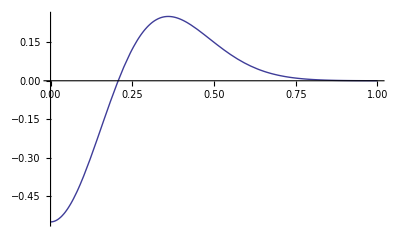

```mathematica
t=.2;mpr=-1;a=mpr;Plot[{h[a,w,t]},{w,0,t b},PlotRange->All]
```

```mathematica
a=-.19901;NIntegrate[Exp[-w^2/2/t^2]/t(Exp[-a xx[w ,t]]xx[w ,t]+Exp[-a xx[-w,t]]xx[-w,t])
,{w,0,t b}]
```

-1.70561×10^-8

```mathematica
mpr=.;
```

```mathematica
ds=Table[as[1/n,b/n],{n,1,60}]
```

{-0.0525742,-0.154073,-0.458295,-0.948096,-1.59442,-2.38981,-3.33203,-4.42028,-5.6542,-7.03363,-8.55848,-10.2287,-12.0442,-14.0051,-16.1112,-18.3626,-20.7594,-23.3014,-25.9886,-28.8212,-31.799,-34.922,-38.1904,-41.604,-45.1629,-48.867,-52.7164,-56.7111,-60.851,-65.1362,-69.5666,-74.1424,-78.8633,-83.7296,-88.7411,-93.8979,-99.1999,-104.647,-110.24,-115.978,-121.861,-127.889,-134.063,-140.381,-146.846,-153.455,-160.21,-167.109,-174.155,-181.345,-188.681,-196.162,-203.788,-211.559,-219.476,-227.538,-235.745,-244.098,-252.596,-261.239}

```mathematica
Integrate[xx[w,1]Exp[-w^2/2],{w,-b,b}]
```

√(π/2) (-2 Erf[b/(√2)]+ⅇ^mpr (Erf[(-1+b)/(√2)]+Erf[(1+b)/(√2)]))

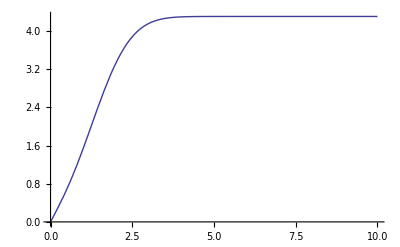

```mathematica
mpr=2/2;Plot[√(π/2) (-2 Erf[b/(√2)]+ⅇ^mpr (Erf[(-1+b)/(√2)]+Erf[(1+b)/(√2)])),{b,0,10}]
```

```mathematica
Exit[]
```

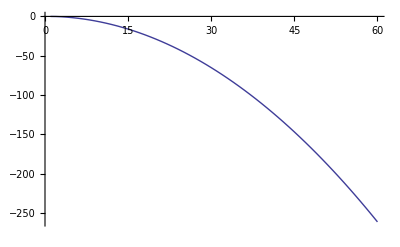

```mathematica
ListLinePlot[ds,PlotRange->All]
```

```mathematica
gs2[a_,t_]:=NIntegrate[Exp[-a(Exp[- t w]-1)-w^2/2](1-Exp[- t w])+Exp[-a(Exp[ t w]-1)-w^2/2](1-Exp[ t w]),{w,0,∞}];
```

```mathematica
Integrate[Exp[t w-w^2/2],{w,-∞,∞}]
```

ⅇ^(t^2/2) √(2 π)

```mathematica
h[w_]:=Exp[-a(Exp[w]-1)](Exp[w]-1)
```

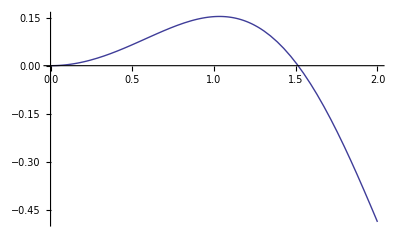

```mathematica
a=.7/2;Plot[h[x]+h[-x]/.x-> w,{w,0,2},PlotRange->All]
```

```mathematica
ie[s_,a_]:=(a(s-1)-1)+(2 a -a^2(s-1))s
a/.Solve[0==ie[s,a],a]
Limit[#,{s->1}]&/@%
```

{(-1+3 s-√(1-2 s+5 s^2))/(2 (-s+s^2)),(-1+3 s+√(1-2 s+5 s^2))/(2 (-s+s^2))}

{{1/2},{∞}}

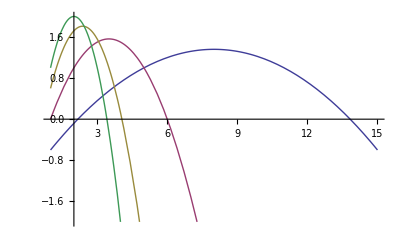

```mathematica
asd=Simplify[Table[ie[s,a],{a,{.2,1/2,.8,1}}]];Plot[asd,{s,1,15},PlotRange->{-2,2}]
```

```mathematica
u[s_]:=-Exp[-a (s-1)](s-1)
```

```mathematica
D[u[s],{s,1}]
D[u[s],{s,2}]
```

-ⅇ^(-a (-1+s))+a ⅇ^(-a (-1+s)) (-1+s)

```mathematica
Simplify[D[Exp[-w^2/2/t^2]/t,t]]
```

(ⅇ^(-w^2/(2 t^2)) (-t^2+w^2))/t^4